```mathematica
(* Γ[c_,a_,b_,met_,coord_] gives Subscript[Γ, ab]^c  for a given metric (nxn matrix) and coordinate system *)
Γ[c_, a_, b_, met_, coord_] := Module[{imet, n}, n = Length[coord]; imet = Inverse[met];
Return[(1/2) Sum[imet[[c, d]] (D[met[[a, d]], coord[[b]]] + D[met[[b, d]], coord[[a]]] - D[met[[a, b]], coord[[d]]]), {d, 1, n}]]]
```

```mathematica
(*This function will take a covariant derivative of an arbitrary tensor field
The result is of the form ∇_var Subscript[T, down]^up where down and up are lists of particular index values
met is the metric and coord is a list of your symbolic coordinates.*)
CovariantD[T_,up_,down_,var_,met_,coord_]:=
Module[{n,indexList,S},
n = Length[coord];
indexList = Join[Table[i,{i,up}],Table[j,{j,down}]];
S = D[Extract[T,indexList],coord[[var]]];
S=S+
Sum[
-Sum[
Γ[d,down[[b]],var,met,coord]Extract[T,ReplacePart[indexList , d, Length[up]+b]],
{d,1,n}],
{b,Length[down]}
]+
Sum[
Sum[
Γ[up[[b]],d,var,met,coord]Extract[T,ReplacePart[indexList , d, b]],
{d,1,n}],
{b,Length[up]}
];
If[up=={} && down =={},S = D[T[[1]],coord[[var]]],S]
]
```

```mathematica
(* R[μ_,ν_,ρ_,σ_,met_,coord_] gives Subscript[R, abc]^d for the given metric *)
R[μ_,ν_,ρ_,σ_,met_,coord_]:=D[Γ[σ,μ,ρ,met,coord],coord[[ν]]]-D[Γ[σ,ν,ρ,met,coord],coord[[μ]]]+Sum[Γ[α,μ,ρ,met,coord] Γ[σ,α,ν,met,coord]-Γ[α,ν,ρ,met,coord] Γ[σ,α,μ,met,coord],{α,1,Length[coord]}]
```

```mathematica
(* R[μ_,ν_,met_,coord_] gives the Ricci Subscript[tensorR, ab]^ for the given metric *)
R[μ_,ρ_,met_,coord_]:=Sum[R[μ,ν,ρ,ν,met,coord],{ν,1,Length[coord]}]
```

```mathematica
(* R[met_,coord_] gives the Ricci Scalar R*)
R[met_,coord_]:=Module[{imet,n},n=Length[coord];imet=Inverse[met];
Return[Sum[imet[[a,b]] R[a,b,met,coord],{a,1,n},{b,1,n}]]]
```

```mathematica
(*Some metrics and coordinates*)
```

```mathematica
(*euclidian cartesian 2 space*)
coord = {x,y};
metric = {{1,0},{0,1}};
```

```mathematica
(*euclidian cartesian 3 space*)
coord = {x,y,z};
metric = {{1,0,0},{0,1,0},{0,0,1}};
```

```mathematica
(*euclidian cartesian n space*)
n = 4;
coord = Table[Superscript[x,i],{i,1,n}];
metric = IdentityMatrix[n];
```

```mathematica
(*euclidian Spherical Polar 3 space*)
coord={r,θ,ϕ};
metric={{1,0,0},{0,r^2,0},{0,0,r^2 Sin[θ]^2}};
```

```mathematica
(*spherical polar paramaterization of a sphere*)
coord = {θ,ϕ};
Metric = {{1,0},{0,radius^2*Sin[θ]^2}};
```

------------------------------------------------ Examples ---------------------------------------------

```mathematica
(*Calculating The christoffel symbol for euclidian spherical polar*)
coord={r,θ,ϕ};
metric={{1,0,0},{0,r^2,0},{0,0,r^2 Sin[θ]^2}};
(*as a matrix ()*)
Table[Simplify[Γ[cc,aa,bb,metric,coord]],{aa,1,Length[coord]},{bb,1,Length[coord]},{cc,1,Length[coord]}]//MatrixForm
```

((0
0
0) | (0
1/r
0) | (0
0
1/r)
(0
1/r
0) | (-r
0
0) | (0
0
Cot[θ])
(0
0
1/r) | (0
0
Cot[θ]) | (-r Sin[θ]^2
-Cos[θ] Sin[θ]
0))

```mathematica
(*or as a really long list*)
Do[Print[Subscript[Superscript[Subscript[Γ, aa],cc], bb] ,"=",Simplify[Γ[cc,aa,bb,metric,coord]]],{aa,1,Length[coord]},{bb,1,Length[coord]},{cc,1,Length[coord]}]
```

(Γ_1^1)_1=0

(Γ_1^2)_1=0

(Γ_1^1)_2=0

(Γ_1^2)_2=0

(Γ_2^1)_1=0

(Γ_2^2)_1=0

(Γ_2^1)_2=0

(Γ_2^2)_2=0

```mathematica
(*Calculating the Covariant Derivative the metric in euclidian spherical polar 3 space*)
coord={r,θ,ϕ};
metric={{1,0,0},{0,r^2,0},{0,0,r^2 Sin[θ]^2}};
upIndices = {};
downIndices = {b,c};
Table[CovariantD[metric,upIndices,downIndices,a,metric,coord],{a,1,3},{b,1,3},{c,1,3}]//MatrixForm
```

((0
0
0) | (0
0
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
0))

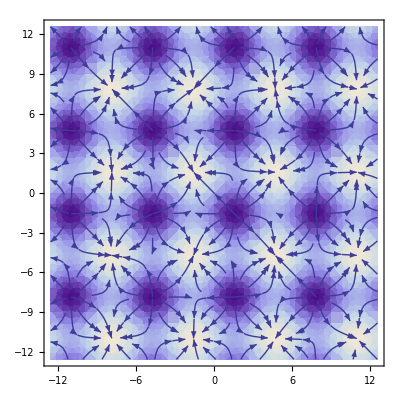

```mathematica
(*euclidian cartesian 2 space*)
coord = {x,y};
metric = {{1,0},{0,1}};
T = {Sin[x-Pi]+Sin[y]};
upIndices = {};
downIndices = {};
DT = Table[CovariantD[T,upIndices,downIndices,a,metric,coord],{a,1,2}];
n = 4*Pi;
Density = DensityPlot[T[[1]],{x,-n,n},{y,-n,n}];
Vector = StreamPlot[DT,{x,-n,n},{y,-n,n}];
Show[Density,Vector]
```